## Defs

First the cream

```mathematica
Cremona[x_,y_,z_]:={y z,z x,x y}
```

degree for symbolic and explicit functions

```mathematica
Clear[Deg]
Deg[ff_Symbol,v_List]:=Deg[ff@@v,v]/;Head[ff@@v]=!=ff
Deg[ff_,v_List]:=Module[{ϵ},If[¬PolynomialQ[ff,v],Print["Warning: non-polynomial: ",ff]];
Exponent[ff/.Thread[v->ϵ v],ϵ]]/;Head[ff]=!=Symbol∨(Head[ff]===Symbol∧DownValues[ff]==={})
```

singular points

```mathematica
Clear[FindP]
FindP[ff_Symbol,v_List]:=FindP[ff@@v,v]/;Head[ff@@v]=!=ff
FindP[ff_,v_List]:=(v/.Solve[ff==0∧D[ff,{v}]==0∧v!=0])/;Head[ff]=!=Symbol∨(Head[ff]===Symbol∧DownValues[ff]==={})
```

the first nonzero series term, showing tangents

```mathematica
Clear[FindTan]
FindTan[ff_Symbol,pp_,v_List]:=FindTan[ff@@v,pp,v]/;Head[ff@@v]=!=ff
FindTan[ff_,pp_,vars_]:=Module[{ϵ,n=1,fu,ser},fu=ff/.MapThread[(#2->#1+ϵ #2)&,{pp,vars}];ser=Series[fu,{ϵ,0,n}];
While[n<=Deg[ff,vars]∧Simplify@Normal[ser]===0,n++;ser=Series[fu,{ϵ,0,n}]];Factor[Normal[ser]/.ϵ->1]]/;Head[ff]=!=Symbol∨(Head[ff]===Symbol∧DownValues[ff]==={})
```

In ℙ^2:[x,y,z],
fundamental points {P, P’, P’’} and exceptional lines {L=𝒱(z), L’=𝒱(y), L’’=𝒱(x)}, where 𝒱 denotes the zero locus.

```mathematica
Clear[𝔉,𝔈];
𝔉={{0,0,1},{0,1,0},{1,0,0}};
𝔈[v_List]:=𝔉.v
```

Check for "good" position i.e.: No exceptional line is tangent to the curve at a fundamental point.

```mathematica
Clear[Good]
Good[f_Symbol,v_List]:=Good[f@@v,v]/;Head[f@@v]=!=f
Good[f_,v_List]:=Module[{fat,fac,sol,pel},
Do[fat=Simplify[f/.Thread[v->𝔉⟦j⟧]];pel=Drop[𝔈[v],{j}];
If[TrueQ[fat!=0],Print["𝔉⟦",j,"⟧ not on curve (f=",fat,")"];Continue[]];
If[fat===0,
Print["𝔉⟦",j,"⟧, f=0. Tangets: " ,fac=FindTan[f,𝔉⟦j⟧,v],". Exceptional lines: ",pel];
susu=(If[SolveAlways[#,v]==={},False,#])&/@Map[PolynomialRemainder[fac,#,#]==0&,pel];
Print["Problem: ",susu];Continue[]];
If[¬TrueQ[fat!=0],Print["𝔉⟦",j,"⟧, f=0 requires 0=",fat,". Tangets: " ,fac=Simplify@FindTan[f,𝔉⟦j⟧,v], ". Exceptional lines: ",pel];
Print[Map[Simplify@PolynomialRemainder[fac,#,#]==0&,pel]],Print["WTF"]]
,{j,3}]]/;Head[f]=!=Symbol∨DownValues[f]==={}
```

Check for “excellent” position i.e.: The curve is in good position, and additionally L intersects (transversally) the curve in n=deg(f) distinct non-fundamental points, and L’ and L’’ each intersect (transversally) the curve in n-r distinct non-fundamental points (no longer symmetric in P, P’, P’’). (r will be the multiplicity of the point under inspection.)

```mathematica
Clear[Excell]
Excell[f_Symbol,v_List]:=Excell[f@@v,v]/;Head[f@@v]=!=f
Excell[f_,v_List]:=Module[{facs,pp,n=Deg[f,v],r=Deg[FindTan[f,𝔉⟦1⟧,v],v]},
Print["L: expected n = ",n," non-fund. points: ",pp=v/.Solve[f==0∧𝔈[v]⟦1⟧==0]/.Thread[v->{1,1,1}],If[pp∩𝔉!={}," - Fundamental problem",""]];
facs=Map[FindTan[f,#,𝕩]&,pp];
Print["Tangents: ",facs," Transversal: ",Map[If[SolveAlways[#==0,v]==={},True,#]&,Simplify@PolynomialRemainder[#,𝔈[v]⟦1⟧,𝔈[v]⟦1⟧]&/@facs]];
Print["L': expected n - r = ",n-r," non-fund. points in addition to 𝔉⟦1⟧: ",pp=v/.Solve[f==0∧𝔈[v]⟦2⟧==0]/.Thread[v->{1,1,1}],If[pp∩𝔉⟦{2,3}⟧!={}," - Fundamental problem",""]];
facs=Map[FindTan[f,#,𝕩]&,pp];
Print["Tangents: ",facs," Transversal: ",Map[If[SolveAlways[#==0,v]==={},True,#]&,Simplify@PolynomialRemainder[#,𝔈[v]⟦2⟧,𝔈[v]⟦2⟧]&/@facs]];
Print["L'': expected n - r = ",n-r," non-fund. points in addition to 𝔉⟦1⟧: ",pp=v/.Solve[f==0∧𝔈[v]⟦3⟧==0]/.Thread[v->{1,1,1}],If[pp∩𝔉⟦{2,3}⟧!={}," - Fundamental problem",""]];
facs=Map[FindTan[f,#,𝕩]&,pp];
Print["Tangents: ",facs," Transversal: ",Map[If[SolveAlways[#==0,v]==={},True,#]&,Simplify@PolynomialRemainder[#,𝔈[v]⟦3⟧,𝔈[v]⟦3⟧]&/@facs]];
]/;Head[f]=!=Symbol∨DownValues[f]==={}
```

## Test Trash

```mathematica
𝕩={x,y,z}
```

{x,y,z}

```mathematica
f1[x_,y_,z_]=f[x,-y,y+z];
```

```mathematica
f1[x_,y_,z_]=8 x^3 y+8 x^3 z+4 x^2 y z-10x y^3-10x y^2 z-3 y^3 z;
```

```mathematica
Good[f1,𝕩]
```

𝔉⟦1⟧, f=0. Tangets: 8 x^3+4 x^2 y-10 x y^2-3 y^3. Exceptional lines: {y,x}

Problem: {False,False}

𝔉⟦2⟧, f=0. Tangets: -10 x-3 z. Exceptional lines: {z,x}

Problem: {False,False}

𝔉⟦3⟧, f=0. Tangets: 8 (y+z). Exceptional lines: {z,y}

Problem: {False,False}

```mathematica
Excell[f1,𝕩]
```

L: expected n = 4 non-fund. points: {{0,1,0},{1,0,0},{1,-2/(√5),0},{1,2/(√5),0}} - Fundamental problem

Tangents: {-10 x-3 z,8 (y+z),-16/25 (10 √5 x+25 y+√5 z),16/25 (10 √5 x-25 y+√5 z)} Transversal: {True,True,True,True}

L': expected n - r = 1 non-fund. points in addition to 𝔉⟦1⟧: {{0,0,1},{1,0,0}} - Fundamental problem

Tangents: {8 x^3+4 x^2 y-10 x y^2-3 y^3,8 (y+z)} Transversal: {True,True}

L'': expected n - r = 1 non-fund. points in addition to 𝔉⟦1⟧: {{0,0,1},{0,1,0}} - Fundamental problem

Tangents: {8 x^3+4 x^2 y-10 x y^2-3 y^3,-10 x-3 z} Transversal: {True,True}

```mathematica
FindP[f1,𝕩]
FindTan[f1,{0,0,1},𝕩]
```

{{0,0,z}}

8 x^3+4 x^2 y-10 x y^2-3 y^3

```mathematica
f1@@Cremona@@𝕩//Simplify
```

x y z^3 (-3 x^3+4 x y^2-10 x^2 (y+z)+8 y^2 (y+z))

```mathematica
FindP[(-3 x^3+4 x y^2-10 x^2 (y+z)+8 y^2 (y+z)),𝕩]
FindTan[(-3 x^3+4 x y^2-10 x^2 (y+z)+8 y^2 (y+z)),{0,0,1},𝕩]
```

{{0,0,z}}

-2 (5 x^2-4 y^2)

```mathematica
Good[(-3 x^3+4 x y^2-10 x^2 (y+z)+8 y^2 (y+z)),𝕩]
```

𝔉⟦1⟧, f=0. Tangets: -2 (5 x^2-4 y^2). Exceptional lines: {y,x}

Problem: {False,False}

𝔉⟦2⟧ not on curve (f=8)

𝔉⟦3⟧ not on curve (f=-3)

```mathematica
Excell[f1,𝕩]
```

L: expected n = 4 points: {{0,1,0},{1,0,0},{1,-2/(√5),0},{1,2/(√5),0}}

Transversal: {True,True,True,True}

L': expected n - r = 1 points other than 𝔉⟦1⟧: {{0,0,1},{1,0,0}}

{8 x^3+4 x^2 y-10 x y^2-3 y^3,8 (y+z)}

Transversal: {True,True}

L'': expected n - r = 1 points other than 𝔉⟦1⟧: {{0,0,1},{0,1,0}}

{8 x^3+4 x^2 y-10 x y^2-3 y^3,-10 x-3 z}

Transversal: {True,True}

```mathematica
Solve[f1[x,y,z]==0∧Echo@𝔈[𝕩]⟦3⟧==0∧𝕩!=0,𝕩]//Simplify[#,{y>0,x>0}]&
pp=(𝕩/.%)/.Thread[𝕩->1]
%//N
```

x

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→0,y→0},{x→0,z→-y}}

{{0,0,1},{0,1,-1}}

{{0.,0.,1.},{0.,1.,-1.}}

```mathematica
FindTan[f1,pp⟦2⟧,𝕩]
%//N
```

y+z

y+z

```mathematica
𝕩/.Solve[f1[x+t y+b z,y+a x+c z,z+d x+e y]==0∧Echo@𝔈[𝕩]⟦1⟧==0∧𝕩!=0]/.Thread[𝕩->1]
Map[FullSimplify@FindTan[f1,#,𝕩]&,%]
𝕩/.Solve[f1[x,y,z]==0∧Echo@𝔈[𝕩]⟦2⟧==0]/.Thread[𝕩->1]
Map[Factor@FindTan[f1,#,𝕩]&,%]
𝕩/.Solve[f1[x,y,z]==0∧Echo@𝔈[𝕩]⟦3⟧==0]/.Thread[𝕩->1]
Map[Factor@FindTan[f1,#,𝕩]&,%]
```

z

{{1,1,0},{1,1,0},{1,1,0},{0,1,0}}

{-1-3 x,-1-3 x,-1-3 x,z}

y

{{0,0,1},{1,0,-1}}

{-((x-y) (x+y)),-x-z}

x

{{0,0,1},{0,1,0}}

{-((x-y) (x+y)),z}

```mathematica
ω[i_]:=Root[#^3+1&,i]
```

```mathematica
PolynomialQuotient[-(x-y)^5+(x+y)^2 z^3,(x+y)^2(3z+3ω[1]x-7ω[1]y)(3z+3ω[2]x-7ω[2]y)(3z+3ω[3]x-7ω[3]y),z]//FullSimplify
```

1/27

```mathematica
f1@@𝕩
```

-(x-y)^5+(x+y)^2 z^3

```mathematica
Solve[f@@𝕩==0,z]//Simplify
```

{{z→-x^3/(x^2-y^2)}}

```mathematica
Collect[PolynomialRemainder[f@@𝕩,γ z+ γ x+β y,z],𝕩,Simplify]
```

-x y^2+(x^2 y β)/γ-(y^3 β)/γ

```mathematica
Inverse@({{1, 0, 0}, {0, -1, 0}, {0, 1, 1}})
```

```mathematica
{{1,0,0},{0,-1,0},{0,1,1}}.𝕩
```

{x,-y,y+z}

## y^2 z-x^2 z-x^3 (or: y^2=x^2+x^3)

```mathematica
𝕩={x,y,z};
Clear[f];
f[x_,y_,z_]=y^2 z-x^2 z-x^3;𝓃=Deg[f,𝕩]
```

3

```mathematica
ContourPlot3D[f[x,y,z]==0,{x,-1,1},{y,-1,1},{z,-1,1},Mesh->None,ContourStyle->Opacity[.6],PlotPoints->50,MaxRecursion->3,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

Singular points.

```mathematica
p1=FindP[f,𝕩]
Map[#/.Solve[#.#==1]&,p1];
sips=Graphics3D[{Darker@Red,PointSize[.02],Point/@%}];
```

{{0,0,z}}

```mathematica
Show[ContourPlot3D[{f[x,y,z]==0,𝕩.𝕩==1},{x,-1.1,1.1},{y,-1.1,1.1},{z,-1.1,1.1},Mesh->{{0}},MeshStyle->{Thick,Darker@Green},MeshFunctions->{{x,y,z}↦({x,y,z}.{x,y,z}-1)-(f[x,y,z])},ContourStyle->{{Opacity[.3]},{Opacity[.1]}},BoundaryStyle->None,MaxRecursion->4,PlotPoints->50,SphericalRegion->True,AxesLabel->{"x","y","z"},Ticks->None],sips]
```

-Graphics3D-

The singular point has multiplicity 2, and distinct tangents. It is ordinary, so genus is clear ((3-1)(3-2))/2-(2(2-1))/2=0, but the construction “should” resolve it completely.

```mathematica
Map[FindTan[f,#,𝕩]&,p1/.Thread[𝕩->1]]
𝓇=Deg[%⟦1⟧,𝕩]
```

{-((x-y) (x+y))}

2

But the curve is not yet in a good position.

```mathematica
Good[f,𝕩]
```

𝔉⟦1⟧, f=0. Tangets: -((x-y) (x+y)). Exceptional lines: {y,x}

Problem: {False,False}

𝔉⟦2⟧, f=0. Tangets: z. Exceptional lines: {z,x}

Problem: {True,False}

𝔉⟦3⟧ not on curve (f=-1)

```mathematica
f1[x_,y_,z_]=f[x,-y,y+z];
Good[f1,𝕩]
```

𝔉⟦1⟧, f=0. Tangets: -((x-y) (x+y)). Exceptional lines: {y,x}

Problem: {False,False}

𝔉⟦2⟧ not on curve (f=1)

𝔉⟦3⟧ not on curve (f=-1)

The line [x1 : y1 : z1] = [1 : t : 0] corresponds to (is the blowup of) [x : y : z] = [0 : 0 : 1] for t∈ℂ_*

```mathematica
Solve[Cremona[x1,y1,z1]=={0,0,z}∧z!=0]
```

{{z→x1 y1,z1→0}}

The result should have a z^𝓇 factor

```mathematica
f02[x1_,y1_,z1_]=f1@@Cremona[x1,y1,z1]//FullSimplify
f2[x1_,y1_,z1_]=(f02[x1,y1,z1]/z1^𝓇//Cancel//FullSimplify)
%/.z1->0//FullSimplify
```

z1^2 (-y1^3 z1+x1^3 (y1+z1)-x1 y1^2 (y1+z1))

-y1^3 z1+x1^3 (y1+z1)-x1 y1^2 (y1+z1)

x1 (x1-y1) y1 (x1+y1)

The reduced curve does not have singularities on the above line [1 : t : 0], or on its own exceptional line z_1=0, although it gains a new ordinary singularity at [0:0:1].

```mathematica
FindP[f2,{x1,y1,z1}]
FindTan[f2,{0,0,1},𝕩]
```

{{0,0,z1}}

x^3-x y^2-y^3

```mathematica
PolynomialRemainder[x^3-x y^2-y^3,x-b y,x]//Simplify
Solve[%==0]
```

(-1-b+b^3) y^3

{{b→Root1.32Root[-1-#1+#1^3&,1]1.324717957244746},{b→Root-0.662-0.562 ⅈRoot[-1-#1+#1^3&,2]-0.662358978622373},{b→Root-0.662+0.562 ⅈRoot[-1-#1+#1^3&,3]-0.662358978622373},{y→0}}

In other words, the only points on the blowup line, that also lie on the curve are non-singular:

```mathematica
Solve[f2[1,t,0]==0∧t!=0]
D[f2[x1,y1,z1],{{x1,y1,z1}}]/.{x1->1,y1->t,z1->0}/.%
```

{{t→-1},{t→1}}

{{-2,-2,1},{2,-2,-1}}

Resolution Graph:

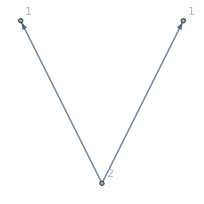

```mathematica
Graph[{1->2,1->3},VertexLabels->{1->2,2->1,3->1},GraphLayout->{"LayeredEmbedding","Orientation"->"Bottom"}]
```

genus

```mathematica
n=Deg[f,𝕩];𝓀={2,1,1};
((n-1)(n-2))/2-Sum[(k(k-1))/2,{k,𝓀}]
```

0

Alternatively, the new curve of degree 4 has an ordinary point of multiplicity 3, so:

```mathematica
((4-1)(4-2))/2-(3(3-1))/2
```

0

### What happens in the affine version?

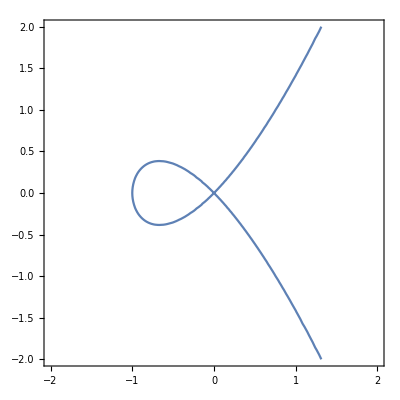

```mathematica
ContourPlot[Y^2-X^2-X^3==0,{X,-2,2},{Y,-2,2}]
```

[x/y:y/z:1]=[x:y:z] | <-> | [y_1 z_1:z_1 x_1:x_1 y_1]=[z_1/x_1:z_1/x_1 x_1/y_1:1]
↕ |  | ↕
(X,Y) | <-> | (U,U V)

```mathematica
Y^2-X^2-X^3+O[ϵ]^3/.{X->ϵ q1,Y->ϵ q2}
Y^2-X^2-X^3/.{X->u, Y-> u v}//Simplify
```

(-q1^2+q2^2) ϵ^2+O[ϵ]^3

u^2 (-1-u+v^2)

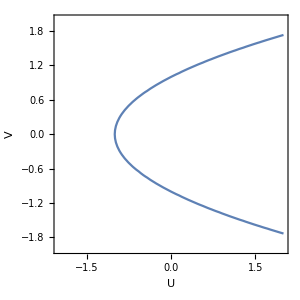
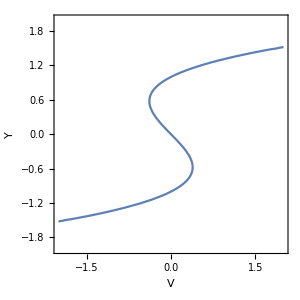

```mathematica
Row[{ContourPlot[v^2-u-1==0,{u,-2,2},{v,-2,2},ImageSize->300,FrameLabel->{U,V}],ContourPlot[v^3-Y-v==0,{Y,-2,2},{v,-2,2},ImageSize->300,FrameLabel->{V,Y}]}]
```

```mathematica
ContourPlot3D[{v^2-X-1==0,v^3-Y-v==0},{X,-2,2},{Y,-2,2},{v,-2,2},PlotPoints->50,ContourStyle->Opacity[.1],Mesh->{{0}},MeshFunctions->{{X,Y,v}↦(v^3-Y-v)-(v^2-X-1)},MeshStyle->{Thick,Darker@Green},AxesLabel->{"X⧦u","Y","v"}]
```

-Graphics3D-

## y^2 z^3-x^5 (or y^2==x^5)

```mathematica
𝕩={x,y,z};
Clear[f];f[x_,y_,z_]=y^2 z^3-x^5;
𝓃=Deg[f,𝕩]
```

5

```mathematica
ContourPlot3D[f[x,y,z]==0,{x,-1,1},{y,-1,1},{z,-1,1},Mesh->None,ContourStyle->Opacity[.6],PlotPoints->50,MaxRecursion->3,AxesLabel->{"x","y","z"}]
```

```mathematica
p1=FindP[f,𝕩]
Map[#/.Solve[#.#==1]&,p1];
sips=Graphics3D[{Darker@Red,PointSize[.02],Point/@%}];
```

{{0,0,z},{0,y,0}}

```mathematica
Show[ContourPlot3D[{f[x,y,z]==0,𝕩.𝕩==1},{x,-1.1,1.1},{y,-1.1,1.1},{z,-1.1,1.1},Mesh->{{0}},MeshStyle->{Thick,Darker@Green},MeshFunctions->{{x,y,z}↦({x,y,z}.{x,y,z}-1)-(f[x,y,z])},ContourStyle->{{Opacity[.3]},{Opacity[.1]}},BoundaryStyle->None,MaxRecursion->4,PlotPoints->50,SphericalRegion->True,AxesLabel->{"x","y","z"},Ticks->None],sips]
```

Two non-ordinary points.

```mathematica
p1/.Thread[𝕩->1]
Map[FindTan[f,#,𝕩]&,%]
𝓇=Map[Deg[#,𝕩]&,%]
```

{{0,0,1},{0,1,0}}

{y^2,z^3}

{2,3}

Resolution of the first point already at 𝔉⟦1⟧

```mathematica
Good[f,𝕩]
```

𝔉⟦1⟧, f=0. Tangets: y^2. Exceptional lines: {y,x}

Problem: {True,False}

𝔉⟦2⟧, f=0. Tangets: z^3. Exceptional lines: {z,x}

Problem: {True,False}

𝔉⟦3⟧ not on curve (f=-1)

```mathematica
f1[x_,y_,z_]=f[x-y,x+y,z]//Simplify
```

-(x-y)^5+(x+y)^2 z^3

```mathematica
FindP[f1,𝕩]
FindTan[f1,{0,0,1},𝕩]
```

{{0,0,z},{x,x,0}}

(x+y)^2

```mathematica
Good[f1,𝕩]
```

𝔉⟦1⟧, f=0. Tangets: (x+y)^2. Exceptional lines: {y,x}

Problem: {False,False}

𝔉⟦2⟧ not on curve (f=1)

𝔉⟦3⟧ not on curve (f=-1)

```mathematica
Excell[f1,𝕩]
```

L: expected n = 5 non-fund. points: {{1,1,0}}

Tangents: {4 z^3} Transversal: {0}

L': expected n - r = 3 non-fund. points in addition to 𝔉⟦1⟧: {{0,0,1},{1,0,1},{1,0,-(-1)^(1/3)},{1,0,(-1)^(2/3)}}

Tangents: {(x+y)^2,-3 x+7 y+3 z,-3 x+7 y+3 (-1)^(2/3) z,-3 x+7 y-3 (-1)^(1/3) z} Transversal: {True,True,True,True}

L'': expected n - r = 3 non-fund. points in addition to 𝔉⟦1⟧: {{0,0,1},{0,1,-1},{0,1,(-1)^(1/3)},{0,1,-(-1)^(2/3)}}

Tangents: {(x+y)^2,-7 x+3 y+3 z,-7 x+3 y+3 (-1)^(2/3) z,-7 x+3 y-3 (-1)^(1/3) z} Transversal: {True,True,True,True}

```mathematica
Clear[f02];f02[x_,y_,z_]=f1@@Cremona@@𝕩//FullSimplify[#,{z>0}]&
f2[x_,y_,z_]=(f02@@𝕩)/z^𝓇⟦1⟧//Cancel//FullSimplify
```

x^3 y^3 (x+y)^2 z^2+(x z-y z)^5

x^3 y^3 (x+y)^2+(x-y)^5 z^3

```mathematica
p2=FindP[f2,𝕩]/.Thread[𝕩->1]
FindTan[f2,#,𝕩]&/@%
```

{{0,0,1},{0,1,0},{1,0,0},{1,-1,0}}

{(x-y)^5,(x-z) (x^2+x z+z^2),(y+z) (y^2-y z+z^2),-(x+y)^2}

Move [1:-1:0] to 𝔉⟦1⟧ and resolve it

```mathematica
f3[x_,y_,z_]=f2[x+z+y,x-z,-y];
FindTan[f3,{0,0,1},𝕩]
Good[f3,𝕩]
```

-(2 x+y)^2

𝔉⟦1⟧, f=0. Tangets: -(2 x+y)^2. Exceptional lines: {y,x}

Problem: {False,False}

𝔉⟦2⟧ not on curve (f=-1)

𝔉⟦3⟧ not on curve (f=4)

```mathematica
f04[x_,y_,z_]=f3@@Cremona@@𝕩//FullSimplify[#,{z>0}]&
f4[x_,y_,z_]=(f04@@𝕩)/z^2//Cancel//FullSimplify
```

z^2 (-x^8 z (2 y+z)^5+y^3 (x+2 y)^2 (-x+z)^3 (y z+x (y+z))^3)

-x^8 z (2 y+z)^5-y^3 (x+2 y)^2 (x-z)^3 (y z+x (y+z))^3

```mathematica
FindP[f4,𝕩]/.Thread[𝕩->1]
```

{{0,1,0},{-2,1,-2},{0,0,1},{1,0,0}}

```mathematica
Solve[f4@@𝕩==0∧𝕩⟦3⟧==0]
```

{{x→0,z→0},{y→0,z→0},{y→-x/2,z→0}}

```mathematica
FindTan[f4,{-2,1,0},𝕩]//FullSimplify
```

-8192 z

Resolution of the second point at [0:1:0]

```mathematica
f5[x_,y_,z_]=f[y-x,z,x+y]
FindTan[f5,{0,0,1},𝕩]
```

-(-x+y)^5+(x+y)^3 z^2

(x+y)^3

```mathematica
Good[f5,𝕩]
```

𝔉⟦1⟧, f=0. Tangets: (x+y)^3. Exceptional lines: {y,x}

Problem: {False,False}

𝔉⟦2⟧ not on curve (f=-1)

𝔉⟦3⟧ not on curve (f=1)

```mathematica
Clear[f06];f06[x_,y_,z_]=f5@@Cremona@@𝕩
f6[x_,y_,z_]=(f06@@𝕩)/z^3//Cancel//FullSimplify
```

-(x z-y z)^5+x^2 y^2 (x z+y z)^3

x^2 y^2 (x+y)^3-(x-y)^5 z^2

```mathematica
FindP[f6,𝕩]
FindTan[f6,{1,-1,0},𝕩]
```

{{0,0,z},{0,y,0},{x,0,0},{x,-x,0}}

-32 z^2

```mathematica
f7[x_,y_,z_]=f6[x+z,x-z+y,x-y]
```

(2 x+y)^3 (x+y-z)^2 (x+z)^2-(x-y)^2 (-y+2 z)^5

```mathematica
Good[f7,𝕩]
```

𝔉⟦1⟧, f=0. Tangets: -32 (x-y)^2. Exceptional lines: {y,x}

Problem: {False,False}

𝔉⟦2⟧ not on curve (f=1)

𝔉⟦3⟧ not on curve (f=8)

```mathematica
Clear[f08];f08[x_,y_,z_]=f7@@Cremona@@𝕩
f8[x_,y_,z_]=(f08@@𝕩)/z^2//Cancel//FullSimplify
```

-(2 x y-x z)^5 (-x z+y z)^2+(x y+y z)^2 (-x y+x z+y z)^2 (x z+2 y z)^3

28 x y^6 z^5+8 y^7 z^5+5 x^3 y^4 z^3 (-8 y^2+8 y z+5 z^2)+2 x^2 y^5 z^3 (-8 y^2+8 y z+19 z^2)-2 x^5 y^2 (y-z) (16 y^4-30 y^3 z+22 y^2 z^2+3 y z^3+z^4)+4 x^4 y^3 z (2 y^4-4 y^3 z-7 y^2 z^2+9 y z^3+2 z^4)+2 x^6 y (32 y^5-77 y^4 z+74 y^3 z^2-38 y^2 z^3+11 y z^4-z^5)+x^7 (-32 y^5+81 y^4 z-82 y^3 z^2+41 y^2 z^3-10 y z^4+z^5)

```mathematica
FindP[f8,𝕩]
FindTan[f8,{1,0,0},𝕩]
```

{{0,0,z},{0,y,0},{x,0,0},{x,-x/2,-x},{x,x,-x},{x,x,x/2}}

-32 y^5+81 y^4 z-82 y^3 z^2+41 y^2 z^3-10 y z^4+z^5

Resolution Graph:

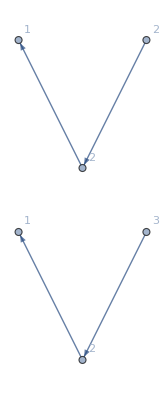

```mathematica
Graph[{1->2,2->3,4->5,5->6},VertexLabels->{1->2,2->2,3->1,4->3,5->2,6->1},GraphLayout->{"LayeredEmbedding","Orientation"->"Bottom"}]
```

genus

```mathematica
𝓀={2,2,1,3,2,1};
((𝓃-1)(𝓃-2))/2-Sum[(k(k-1))/2,{k,𝓀}]
```

0

## y^2 z^4-x^2 y^4+x^4 z^2

```mathematica
𝕩={x,y,z};
f[x_,y_,z_]=y^2 z^4-x^2 y^4+x^4 z^2;𝓃=Deg[f,𝕩]
```

6

```mathematica
ContourPlot3D[f[x,-y,y+z]==0,{x,-1,1},{y,-1,1},{z,-1,1},Mesh->None,ContourStyle->Opacity[.6],PlotPoints->50,MaxRecursion->3,AxesLabel->{"x","y","z"}]
```

```mathematica
p1=DeleteDuplicates@FindP[f,𝕩]
Map[#/.Solve[#.#==1]&,p1];
sips=Graphics3D[{Darker@Red,PointSize[.02],Point/@%}];
```

{{0,0,z},{0,y,0},{x,0,0}}

```mathematica
Show[ContourPlot3D[{f[x,y,z]==0,𝕩.𝕩==1},{x,-1.1,1.1},{y,-1.1,1.1},{z,-1.1,1.1},Mesh->{{0}},MeshStyle->{Thick,Darker@Green},MeshFunctions->{{x,y,z}↦({x,y,z}.{x,y,z}-1)-(f[x,y,z])},ContourStyle->{{Opacity[.3]},{Opacity[.1]}},BoundaryStyle->None,MaxRecursion->4,PlotPoints->50,SphericalRegion->True,AxesLabel->{"x","y","z"},Ticks->None],sips]
```

```mathematica
p1/.Thread[𝕩->1]
Map[FindTan[f,#,𝕩]&,%]
𝓇=Map[Deg[#,𝕩]&,%]
```

{{0,0,1},{0,1,0},{1,0,0}}

{y^2,-x^2,z^2}

{2,2,2}

```mathematica
Good[f,𝕩]
```

𝔉⟦1⟧, f=0. Tangets: y^2. Exceptional lines: {y,x}

Problem: {True,False}

𝔉⟦2⟧, f=0. Tangets: -x^2. Exceptional lines: {z,x}

Problem: {False,True}

𝔉⟦3⟧, f=0. Tangets: z^2. Exceptional lines: {z,y}

Problem: {True,False}

## (ζ̇)^4==ζ^3(ζ-1)^3 or y^4 x^2-z^3(z-x)^3

```mathematica
𝕩={x,y,z};
f[x_,y_,z_]=y^4 x^2-z^3(z-x)^3;𝓃=Deg[f,𝕩]
```

6

```mathematica
ContourPlot3D[f[x,y,z]==0,{x,-1,1},{y,-1,1},{z,-1,1},Mesh->None,ContourStyle->Opacity[.6],PlotPoints->50,MaxRecursion->3,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
p1=DeleteDuplicates@FindP[f,𝕩]
Map[#/.Solve[#.#==1]&,p1];
sips=Graphics3D[{Darker@Red,PointSize[.02],Point/@%}];
```

{{z,0,z},{0,y,0},{x,0,0}}

```mathematica
Show[ContourPlot3D[{f[x,y,z]==0,𝕩.𝕩==1},{x,-1.1,1.1},{y,-1.1,1.1},{z,-1.1,1.1},Mesh->{{0}},MeshStyle->{Thick,Darker@Green},MeshFunctions->{{x,y,z}↦({x,y,z}.{x,y,z}-1)-(f[x,y,z])},ContourStyle->{{Opacity[.3]},{Opacity[.1]}},BoundaryStyle->None,MaxRecursion->4,PlotPoints->50,SphericalRegion->True,AxesLabel->{"x","y","z"},Ticks->None],sips]
```

-Graphics3D-

```mathematica
p1/.Thread[𝕩->1]
Map[FindTan[f,#,𝕩]&,%]
𝓇=Map[Deg[#,𝕩]&,%]
```

{{1,0,1},{0,1,0},{1,0,0}}

{(x-z)^3,x^2,z^3}

{3,2,3}

```mathematica
Good[f[x+ y,z,2y-x],𝕩]
```

𝔉⟦1⟧, f=0. Tangets: (x+y)^2. Exceptional lines: {y,x}

Problem: {False,False}

𝔉⟦2⟧ not on curve (f=-8)

𝔉⟦3⟧ not on curve (f=-8)

```mathematica
Good[f[z,x+y,2y-x],𝕩]
```

𝔉⟦1⟧, f=0. Tangets: -(x-2 y)^3. Exceptional lines: {y,x}

Problem: {False,False}

𝔉⟦2⟧ not on curve (f=-64)

𝔉⟦3⟧ not on curve (f=-1)

```mathematica
Good[f[z+y,y,z-x],𝕩]
```

𝔉⟦1⟧, f=0. Tangets: (x+y)^3. Exceptional lines: {y,x}

Problem: {False,False}

𝔉⟦2⟧ not on curve (f=1)

𝔉⟦3⟧ not on curve (f=-1)

```mathematica
Excell[f[x+y,z,2y-x],𝕩]
```

L: expected n = 6 non-fund. points: {{1,1/2,0},{1,2,0}}

Tangents: {-27/8 (x-2 y)^3,27 (2 x-y)^3} Transversal: {True,True}

L': expected n - r = 4 non-fund. points in addition to 𝔉⟦1⟧: {{0,0,1},{1,0,-2^(3/4)},{1,0,-ⅈ 2^(3/4)},{1,0,ⅈ 2^(3/4)},{1,0,2^(3/4)}}

Tangents: {(x+y)^2,-4 (8 x-19 y+4 2^(1/4) z),-4 (8 x-19 y-4 ⅈ 2^(1/4) z),-4 (8 x-19 y+4 ⅈ 2^(1/4) z),-4 (8 x-19 y-4 2^(1/4) z)} Transversal: {True,True,True,True,True}

L'': expected n - r = 4 non-fund. points in addition to 𝔉⟦1⟧: {{0,0,1},{0,1,-2^(3/4)},{0,1,-ⅈ 2^(3/4)},{0,1,ⅈ 2^(3/4)},{0,1,2^(3/4)}}

Tangents: {(x+y)^2,4 (19 x-8 y-4 2^(1/4) z),4 (19 x-8 y+4 ⅈ 2^(1/4) z),4 (19 x-8 y-4 ⅈ 2^(1/4) z),4 (19 x-8 y+4 2^(1/4) z)} Transversal: {True,True,True,True,True}

```mathematica
f1[x_,y_,z_]=f[x+y,z,2y-x];
```

```mathematica
f2[x1_,y1_,z1_]=1/z1^2 f1@@Cremona@@{x1,y1,z1}//FullSimplify
```

x1^4 y1^4 (x1+y1)^2-(x1-2 y1)^3 (2 x1-y1)^3 z1^4

```mathematica
FindP[f2,{x1,y1,z1}]
FindTan[f2,{1,-1,0},{x1,y1,z1}]//FullSimplify
```

{{0,0,z1},{0,y1,0},{x1,0,0},{x1,-x1,0}}

(x1+y1)^2

```mathematica
Good[f3[x_,y_,z_]=f2[x+z,y-z,y],𝕩]
```

𝔉⟦1⟧, f=0. Tangets: (x+y)^2. Exceptional lines: {y,x}

Problem: {False,False}

𝔉⟦2⟧ not on curve (f=-8)

𝔉⟦3⟧, f=0. Tangets: -7 y^4-4 y^3 z+6 y^2 z^2-4 y z^3+z^4. Exceptional lines: {z,y}

Problem: {False,False}

```mathematica
f4[x_,y_,z_]=(f3@@Cremona@@𝕩)/z^2//Cancel//FullSimplify
```

x^4 (x^4 y^8 (x+y)^2-4 x^3 (x-y) y^7 (x+y)^2 z-x^2 y^6 (723 x^4+4 x^3 y+20 x^2 y^2+4 x y^3-6 y^4) z^2+x (x-y) y^5 (2183 x^4+12 x^3 y+32 x^2 y^2+12 x y^3-4 y^4) z^3+y^4 (-2672 x^6+5575 x^5 y-2668 x^4 y^2+40 x^3 y^3+5 x^2 y^4-14 x y^5+y^6) z^4+(x-y) y^3 (1701 x^5-3884 x^4 y+1689 x^3 y^2-32 x^2 y^3-12 x y^4+4 y^5) z^5+y^2 (-594 x^6+2727 x^5 y-4287 x^4 y^2+2723 x^3 y^3-614 x^2 y^4-4 x y^5+6 y^6) z^6+(x-y) y (108 x^5-540 x^4 y+891 x^3 y^2-536 x^2 y^3+116 x y^4+4 y^5) z^7+(-8 x^6+60 x^5 y-174 x^4 y^2+245 x^3 y^3-173 x^2 y^4+62 x y^5-7 y^6) z^8)

```mathematica
Solve[f4[1,t,0]==0∧t!=0]
```

{{t→-1},{t→-1}}

```mathematica
FindTan[f4,{1,-1,0},𝕩]
```

(x+y-27 z) (x+y+27 z)

```mathematica
f5[x_,y_,z_]=f[z,x+y,2y-x];
f6[x_,y_,z_]=(f5@@Cremona@@𝕩)/z^3//Simplify
```

x^2 y^2 (x+y)^4 z+(2 x-y)^3 (x (y-2 z)+y z)^3

```mathematica
FindP[f6,𝕩]
```

{{0,y,0},{-y,y,y/3},{0,0,z},{x,0,0}}

```mathematica
Solve[f6@@𝕩==0∧𝕩=={1,t,0}∧t!=0]
```

{{t→2,x→1,y→2,z→0}}

```mathematica
FindTan[f6,{1,2,0},𝕩]
```

324 z

```mathematica
f7[x_,y_,z_]=1/z^3(f[z+y,y,z-x]/.Thread[𝕩->Cremona@@𝕩])//FullSimplify
```

y^3 (x+y)^3 (x-z)^3+x^6 z (y+z)^2

```mathematica
FindP[f7,𝕩]
Solve[f7@@𝕩==0∧𝕩=={1,t,0}∧t!=0]
FindTan[f7,{1,-1,0},𝕩]
```

{{0,y,0},{-y,y,-y},{0,0,z},{x,0,0}}

{{t→-1,x→1,y→-1,z→0}}

z

```mathematica
𝓀={2,2,2,3,1,3,1};
((𝓃-1)(𝓃-2))/2-Sum[(k(k-1))/2,{k,𝓀}]
```

1